phi=90-theta

(2 π)/9

1.53209

(59 π)/180

1.02036

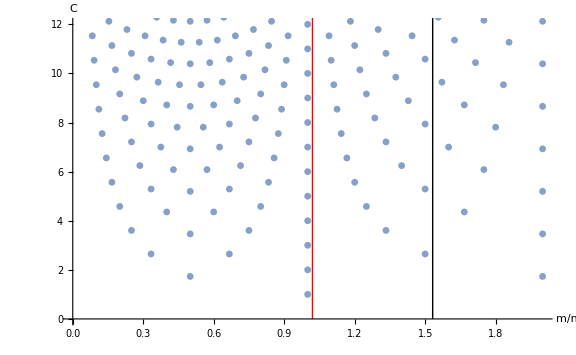

```mathematica
x=40*Pi/180
eq=N[Sqrt[3]Tan[Pi/2-x]/2+1/2]
cs=Table[{m/n,Sqrt[m^2+n^2-m n]},{m,1,40},{n,1,40}];
line=Line[{{eq,0},{eq,50}}];
csnum=Partition[Flatten[Table[{m, n, N[m/n],N[Sqrt[m^2+n^2-m n]]},{m,1,50},{n,1,50}]], 4];

x=59*Pi/180
eq=N[Sqrt[3]Tan[Pi/2-x]/2+1/2]
cs=Table[{m/n,Sqrt[m^2+n^2-m n]},{m,1,40},{n,1,40}];
line1=Line[{{eq,0},{eq,50}}];
csnum=Partition[Flatten[Table[{m, n, N[m/n],N[Sqrt[m^2+n^2-m n]]},{m,1,50},{n,1,50}]], 4];

ListPlot[cs,AxesLabel->{Style["m/n", Bold, 22],Style["C",Bold, 22]}, Epilog->{{Black,Thick,line},{Red,Thick,line1}}, PlotRange->{{0,2},{0,12}},TicksStyle->Large,ImageSize->Large,PlotMarkers->{Graphics[{Opacity[0.75],ColorData[97][1],Disk[]}],Small}]
```

```mathematica
Export["/Users/jessicasun/Documents/GitHub/062122-bennett-draft/main_figs/magic.svg",%,"SVG"]
```

/Users/jessicasun/Documents/GitHub/062122-bennett-draft/main_figs/magic.svg